```mathematica
k=25;
g=10;
l=2;
e=12.5
a0=Pi/2;
b=2.1;
d=1;
```

12.5

```mathematica
s=NDSolve[{r''[t]==r[t]*a'[t]^2+g*Cos[a[t]]-k*(r[t]-l),(2*r'[t]*a'[t]+r[t]*a''[t])==-g*Sin[a[t]],r'[0]==d,r[0]==b,a[0]==a0,a'[0]==-Sqrt[(2e+2g*r[0]*Cos[a[0]]-k(r[0]-l)^2-r'[0]^2)/(r[0]^2)]},{r,a},{t,0,10000}]
data=Block[{},Reap[NDSolve[{r''[t]==r[t]*a'[t]^2+g*Cos[a[t]]-k*(r[t]-l),(2*r'[t]*a'[t]+r[t]*a''[t])==-g*Sin[a[t]],r'[0]==d,r[0]==b,a[0]==a0,a'[0]==-Sqrt[(2e+2g*r[0]*Cos[a[0]]-k(r[0]-l)^2-r'[0]^2)/(r[0]^2)],WhenEvent[a'[t]==0,Sow[{r[t],r'[t]}]]},{},{t,0,10000},MaxSteps->∞]]][[-1,1]];
```

{{r→InterpolatingFunction[{{0., 10000.}}, <>],a→InterpolatingFunction[{{0., 10000.}}, <>]}}

```mathematica
s2=NDSolve[{r1''[t]==r1[t]*a1'[t]^2+g*Cos[a1[t]]-k*(r1[t]-l),(2*r1'[t]*a1'[t]+r1[t]*a1''[t])==-g*Sin[a1[t]],r1'[0]==d,r1[0]==b-0.001,a1[0]==a0,a1'[0]==-Sqrt[(2e+2g*r1[0]*Cos[a1[0]]-k(r1[0]-l)^2-r1'[0]^2)/(r1[0]^2)]},{r1,a1},{t,0,10000}]
```

{{r1→InterpolatingFunction[{{0., 10000.}}, <>],a1→InterpolatingFunction[{{0., 10000.}}, <>]}}

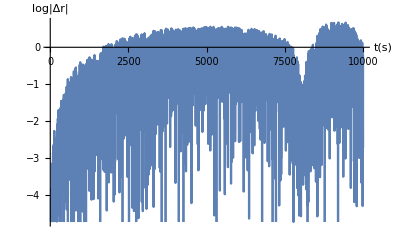

```mathematica
Plot[Log[Abs[Evaluate[r[t]/.s]-Evaluate[r1[t]/.s2]]],{t,0,10000},AxesLabel->{"t(s)","log|Δr|"}]
```

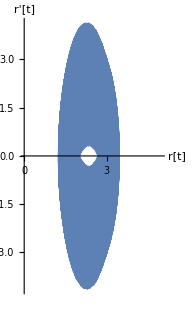

```mathematica
ParametricPlot[Evaluate[{r[t],r'[t]}/.s],{t,0,200},PlotRange->{{0,5},All}, AxesLabel->{"r[t]","r'[t]"}]
```

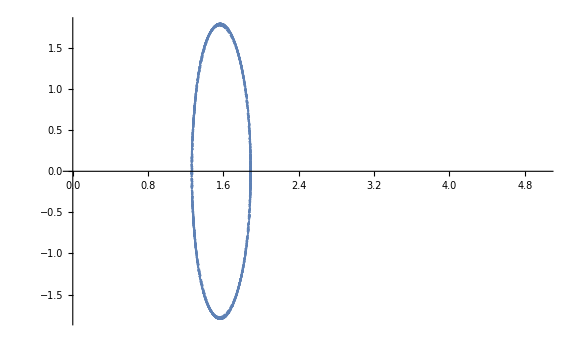

```mathematica
ListPlot[data,ImageSize->Large,PlotRange->{{0,5},All},PlotStyle->PointSize[0.0025]]
```

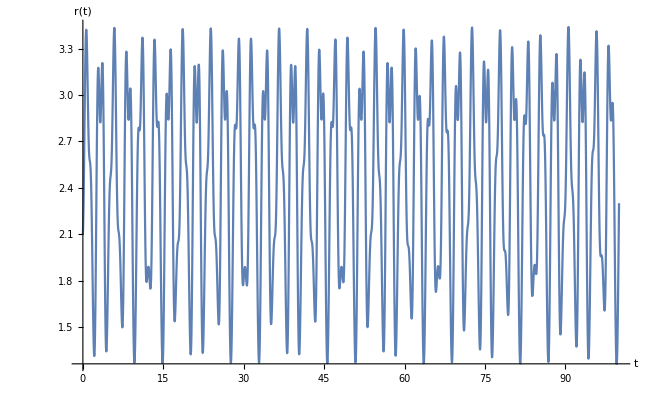

```mathematica
Plot[Evaluate[r[t]/.s],{t,0,100},AxesLabel->{t,r[t]}]
```